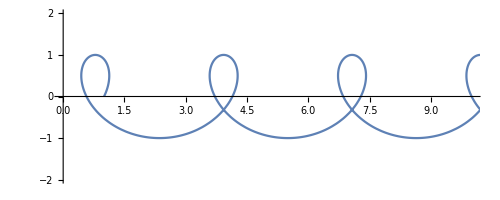

```mathematica
ParametricPlot[{Cos[t] + 0.5 t, Sin[t]}, {t, 0, 10 π}, PlotRange->{{0,10}, {-2, 2}}]
```

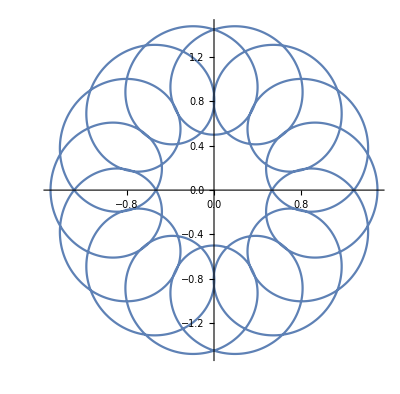

```mathematica
ParametricPlot[{Cos[t] + 0.5 Cos[15t], Sin[t] + 0.5Sin[15t]}, {t, 0, 2π}]
```

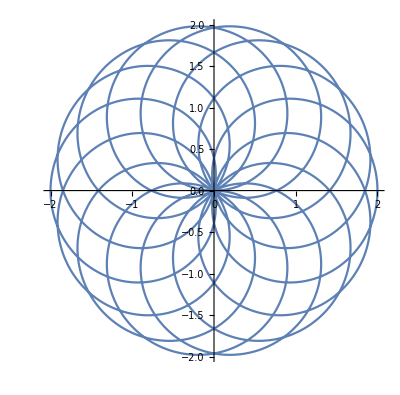

```mathematica
ParametricPlot[{Cos[t] + Cos[15t], Sin[t] + Sin[15t]}, {t, 0, 2π}]
```

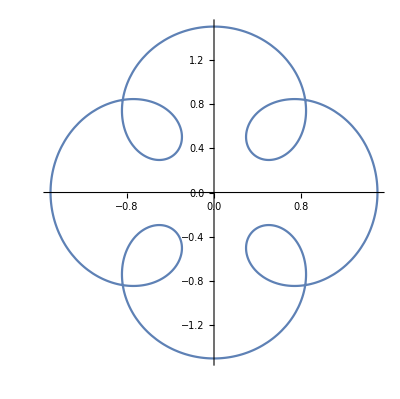

```mathematica
ParametricPlot[{Cos[t] + 0.5 Cos[5t], Sin[t] + 0.5Sin[5t]}, {t, 0, 2π}]
```

```mathematica
Manipulate[ParametricPlot[{Cos[t] + 0.5 Cos[5t], Sin[t] + 0.5Sin[5t]}, {t, 0, time}, PlotRange->{{-1.5, 1.5}, {-1.5, 1.5}}], {time, 0.001, 0.5 π}]
```

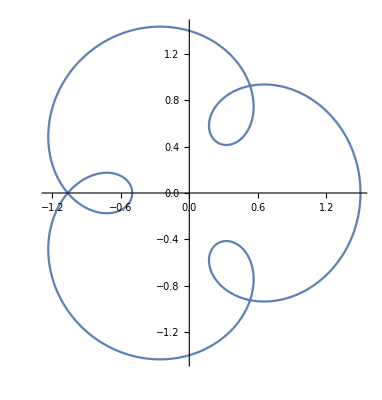

```mathematica
ParametricPlot[{Cos[t] + 0.5 Cos[4t], Sin[t] + 0.5Sin[4t]}, {t, 0, 2π}]
```

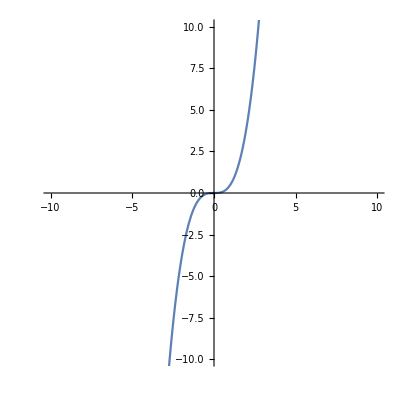

```mathematica
ParametricPlot[{t, 0.5 t^3}, {t, -10, 10}, PlotRange->{{-10, 10}, {-10, 10}}]
```

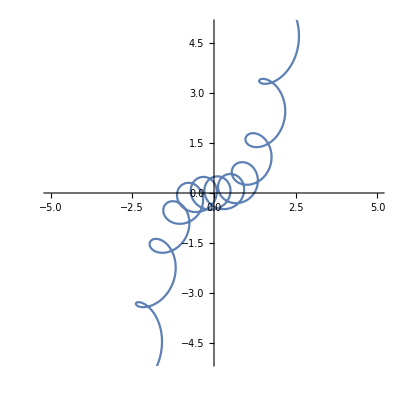

```mathematica
ParametricPlot[{t + 0.5Cos[15t], 0.5 t^3 + 0.5 Sin[15 t]}, {t, -10, 10}, PlotRange->{{-5, 5}, {-5, 5}}]
```

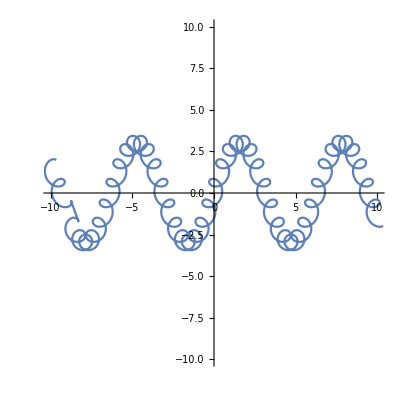

```mathematica
ParametricPlot[{t + 0.5Cos[15t], 3Sin[t] + 0.5Sin[15 t]}, {t, -10, 10}, PlotRange->{{-10, 10}, {-10, 10}}]
```

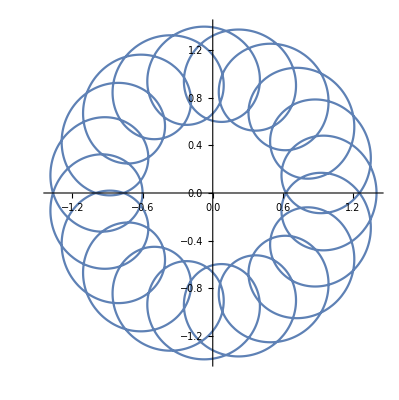

```mathematica
ParametricPlot[{Cos[t] + 0.4Cos[20t], Sin[t] + 0.4Sin[20t]}, {t, 0, 2π}]
```

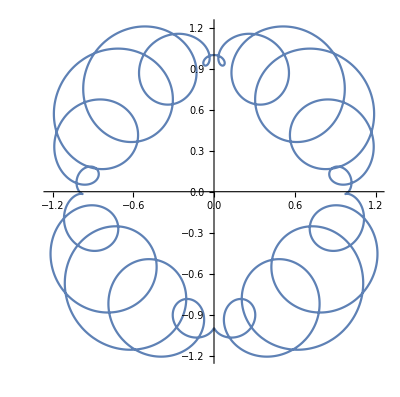

```mathematica
ParametricPlot[{Cos[t] + 0.4*Sin[2t]* Cos[20t], Sin[t] + 0.4*Sin[2t]*Sin[20t]}, {t, 0, 2π}]
```

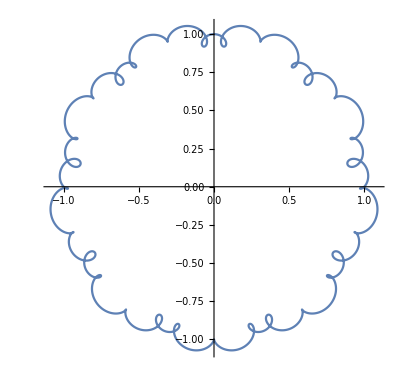

```mathematica
ParametricPlot[{Cos[t] + 0.1*Sin[10t]* Cos[20t], Sin[t] + 0.1*Sin[10t]*Sin[20t]}, {t, 0, 2π}]
```

```mathematica
gif = Animate[Plot[Sin[3 t + time], {t, 0, 2Pi}, PlotRange->{{0, 2 Pi}, {-1, 1}}], {time, 0, 6 Pi}]
```

```mathematica
Export["sineTimed.swf",gif]
```

sineTimed.swf

```mathematica
SystemOpen["sineTimed.swf"]
```

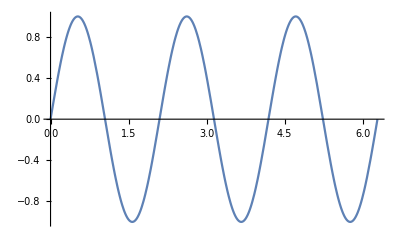
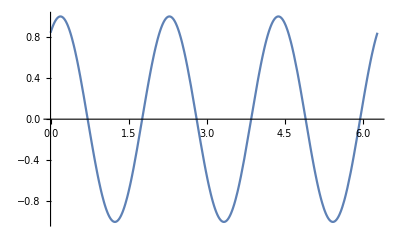
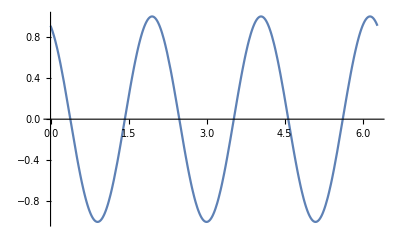
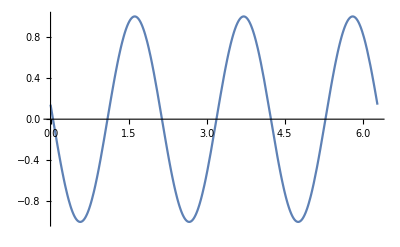
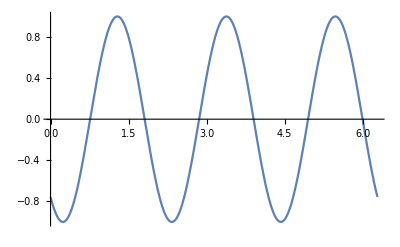
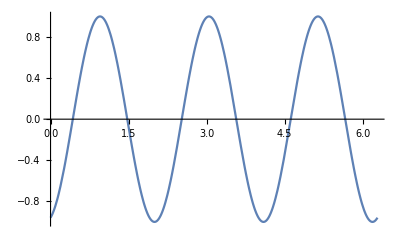
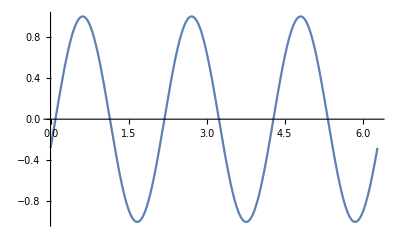
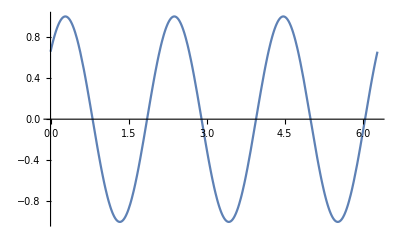

sin.gif

```mathematica
gif2 = Table[Plot[Sin[3 t + time], {t, 0, 2Pi}, PlotRange->{{0, 2 Pi}, {-1, 1}}], {time, 0, 6 Pi}]
Export["sin.gif",gif2]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["sin.gif"]]]
```

```mathematica
SystemOpen["sin.gif"]
```

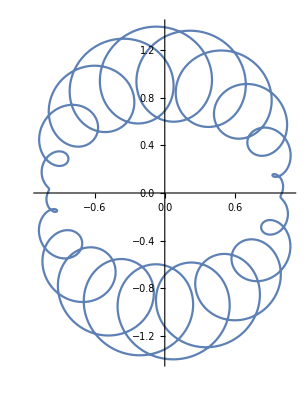

```mathematica
ParametricPlot[{Cos[t] + 0.4*Sin[t]* Cos[20t], Sin[t] + 0.4*Sin[t]*Sin[20t]}, {t, 0, 2π}]
```

```mathematica
Animate[ParametricPlot[{Cos[t ] + 0.4*Sin[t+ time]* Cos[20t], Sin[t ] + 0.4*Sin[t + time]*Sin[20t]}, {t, 0, 2π}, PlotRange->{-1.5, 1.5}], {time, 0,  2Pi}]
```

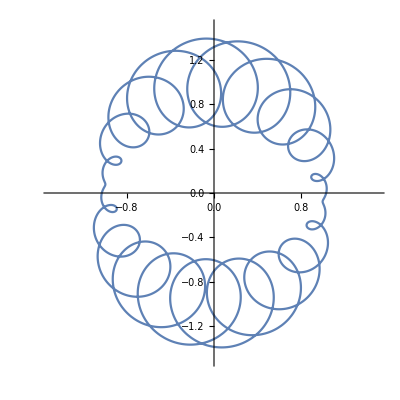
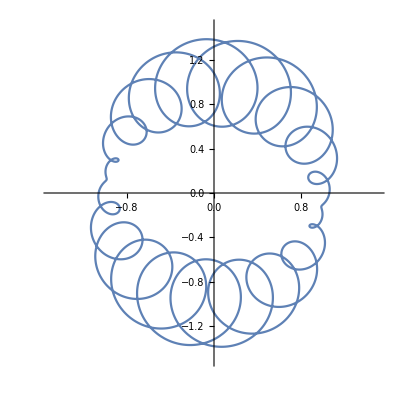
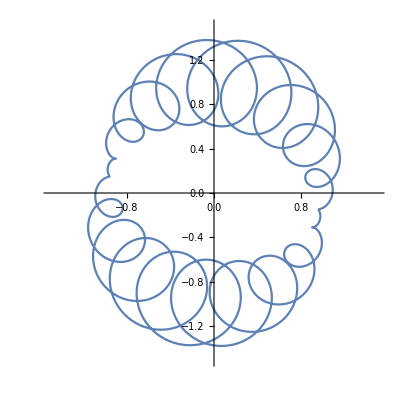
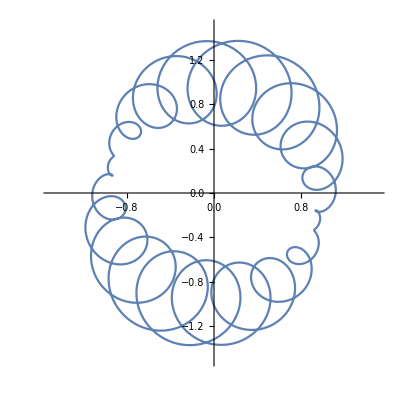
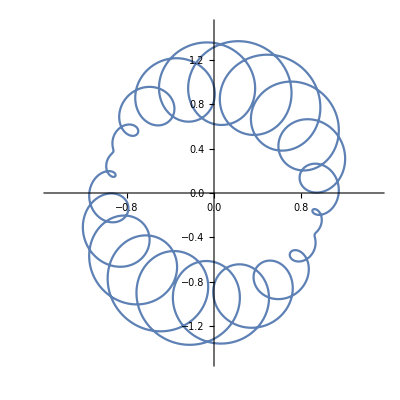
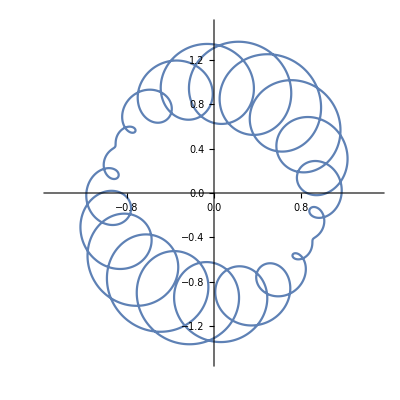
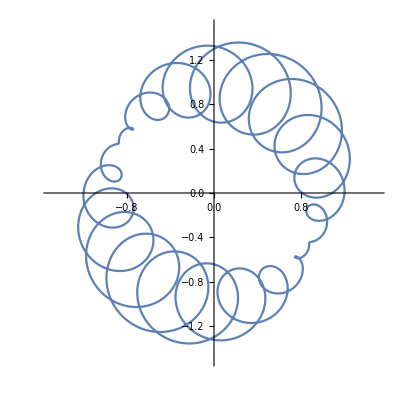
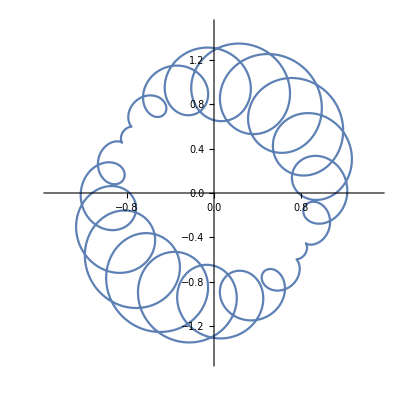
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

test.mov

```mathematica
time2=4Pi + 1;fps=24;da = 1 / time2;a0=da;
frames=Table[ParametricPlot[{Cos[t ] + 0.4*Sin[t+ time]* Cos[20t], Sin[t ] + 0.4*Sin[t + time]*Sin[20t]}, {t, 0, 2π}, PlotRange->{-1.5, 1.5}],{time,a0,da*time2*fps,da}]
Export["test.mov",frames,"FrameRate"->fps]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test.mov"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test.mov"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test.mov"]]]
```